```mathematica
deqns={θ1'[t]==ω1[t],
ω1'[t]==(-g(2 m1 + m2)Sin[θ1[t]]-m2 g Sin[θ1[t]-2 θ2[t]]-2 Sin[θ1[t]-θ2[t]] m2 (ω2[t]^2 L2 + ω1[t]^2 L1 Cos[θ1[t]-θ2[t]]))/(L1(2m1+m2 -m2 Cos[2 θ1[t] - 2θ2[t]])),
θ2'[t]==ω2[t],
ω2'[t]==(2 Sin[θ1[t]-θ2[t]](ω1[t]^2 L1 (m1 + m2) + g(m1+m2)Cos[θ1[t]]+ω2[t]^2 L2 m2 Cos[θ1[t]-θ2[t]]))/(L2(2m1+m2 -m2 Cos[2 θ1[t] - 2θ2[t]])) };
```

```mathematica
ics = {ω1[0]==0,ω2[0]==0, θ1[0]==π/2,θ2[0]==0};
```

```mathematica
params={g->9.81,L1->1, L2->1, m1->1,m2->1};
```

```mathematica
soldp=First[NDSolve[{deqns,ics}/.params,{θ1, θ2, ω1, ω2},{t,0,15}]];
```

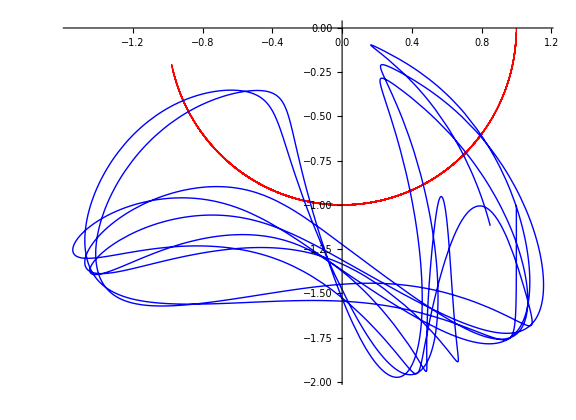

```mathematica
ParametricPlot[Evaluate[{{L1 Sin[θ1[t]],-L1 Cos[θ1[t]]},{L1 Sin[θ1[t]]+L2 Sin[θ2[t]],-L1 Cos[θ1[t]]-L2 Cos[θ2[t]]}}/.Join[soldp,params]],{t,0,15},PlotStyle->{Red,Blue},ImageSize->Large]
```

```mathematica
Table[{θ1[t], ω1[t], θ2[t], ω2[t]}/.soldp, {t,0,15,1}]
```

{{1.5708,0.,0.,0.},{-0.883696,2.09455,-0.471005,-6.12116},{0.829721,0.0327718,-1.213,3.72156},{-0.556896,0.94528,2.26612,0.523034},{0.745183,-2.22757,-1.08521,-3.5349},{-0.917127,2.98843,0.787568,1.01784},{1.27475,-2.15821,-0.349616,0.86353},{-0.869447,4.09303,-0.751274,-5.81162},{0.0689359,-2.54919,1.27355,4.53345},{-0.521796,1.94559,1.21512,-3.38815},{0.104991,-1.70303,-2.22075,0.591468},{0.118426,4.52891,0.907663,-2.43006},{0.262303,-6.05017,0.174655,5.18184},{-0.0387344,3.06063,-1.60292,-0.495557},{-0.217135,-0.637768,2.28281,1.79714},{-0.142261,1.64574,1.44256,-4.01627}}